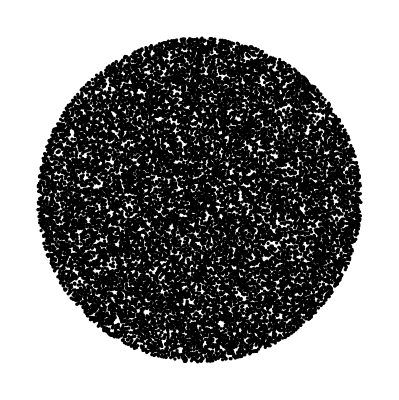

```mathematica
Graphics[Table[
Disk[Sqrt[Random[]]{Cos[#],Sin[#]}&@(2Pi Random[]),.01],20000]]
```

The area of a random triangle in the square

```mathematica
Plus@@Table[1/2(#.#)&@(Cross@@Table[Random[],2,3]),10000]/10000
```

0.144609

What is the probability that four points randomly chosen in a square bound a triangle (or any convex polygon)

```mathematica
inconvexpolygon[x_,polyverts_]:=
(pp = Append[#,0]&/@polyverts;
xx = Append[x,0];
pone=Mod[#,Length[polyverts]]+1&;
And@@Table[0>((pp[[pone@i]]-pp[[i]])×(xx-pp[[i]]))[[3]],{i,Length[polyverts]}])
```

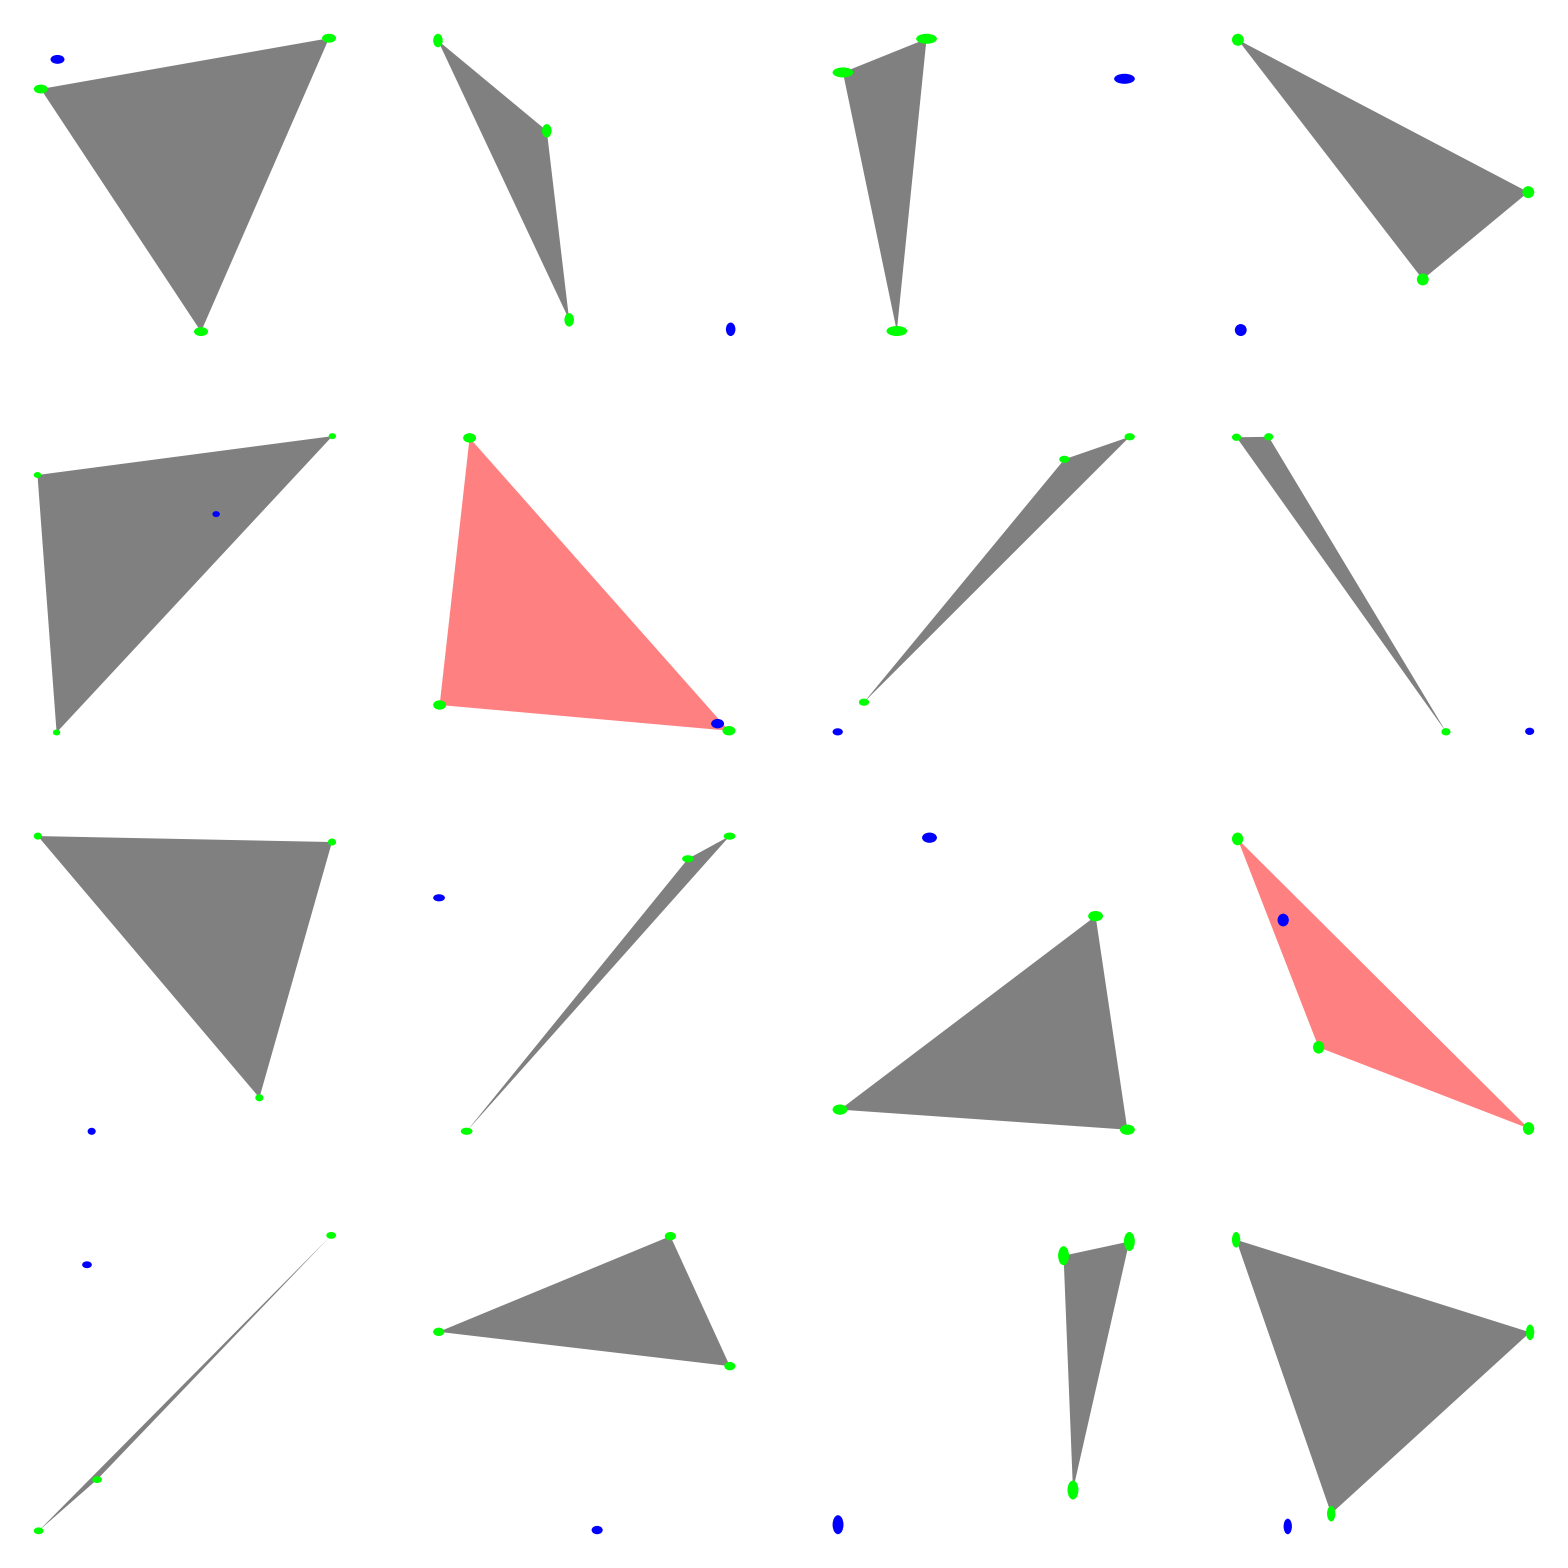

```mathematica
GraphicsGrid[Table[x ={ Random[],Random[]};
polyverts = Table[{Random[],Random[]},3];Graphics[{ 
If[inconvexpolygon[x,polyverts],Pink,Gray],Polygon@polyverts,Blue,Disk[x,.01],Green,Disk[#,.01]&/@polyverts}],4,4]]
```

```mathematica
Plus@@Table[If[inconvexpolygon[{ Random[],Random[]},Table[{Random[],Random[]},3]],1,0],10000]
```

370

```mathematica
Plus@@Table[
ppts = Table[Random[],4,2];
If[
Or@@Table[inconvexpolygon[#[[1]],Drop[#,1]]&@RotateRight[ppts,i],{i,0,3}],1,0],100000]
```

15283

However, this is about half of the right value!

https : // mathworld . wolfram . com/SylvestersFour - PointProblem . html